# Quantum Computation: Overview

The  full text of Chapter 2 of the book “A Quantum Computation Workbook” is available. To read it in PDF, please click the button: "Full text of Chapter 2 in PDF".

```mathematica
<<Q3`
<<Q3`Gray`
<<WorkbookTools`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Quantum computation is an implementation of an arbitrary unitary operation on a finite collection of qubits. It is typically depicted in a quantum circuit model.

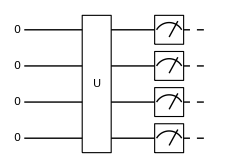

```mathematica
$n=4;
SS=S[Range[$n],None];
qc=QuissoCircuit[
{LogicalForm[Ket[],SS]},"Spacer",
{One[SS],"Label"->"U"},"Spacer",
Measurement[SS]
]
```

## Single-Qubit Gates

### Pauli Gates

The Pauli X gate is represented by S[…,1].

```mathematica
S[1]
```

S^x

It corresponds to the Pauli X matrix.

```mathematica
Matrix[S[1]]//MatrixForm
```

(0 | 1
1 | 0)

In the quantum circuit model, it is denoted by the following quantum circuit element.

```mathematica
QuissoCircuit[S[1]]
```

-Graphics-

Operating on the logical basis states, it flips the states and is similar to the classical logical gate NOT.

```mathematica
bs=Basis[S];
out=S[1]**bs;
Thread[bs->out]//LogicalForm//TableForm
```

0_S→1_S
1_S→0_S

Operating on a superposition state, it flips the state “simultaneously”.

```mathematica
in=Ket[]c[0]+Ket[S->1]c[1];
in//LogicalForm
out=S[1]**in;
out//LogicalForm
```

c_0 0_S+c_1 1_S

c_1 0_S+c_0 1_S

The Pauli Z gate is represented by S[…,3].

```mathematica
S[3]
```

S^z

It corresponds to the Pauli Z matrix.

```mathematica
Matrix[S[3]]//MatrixForm
```

(1 | 0
0 | -1)

In the quantum circuit model, it is denoted by the following quantum circuit element.

```mathematica
QuissoCircuit[S[3]]
```

-Graphics-

Operating on the logical basis states, it “flips the phase”, that is, it changes the phase factor to -1 of the logical basis state 1.

```mathematica
bs=Basis[S];
out=S[3]**bs;
Thread[bs->out]//LogicalForm//TableForm
```

0_S→0_S
1_S→-1_S

Here is an example how the Pauli Z gate acts on a superposition state.

```mathematica
in=Ket[]c[0]+Ket[S->1]c[1];
in//LogicalForm
out=S[3]**in;
out//LogicalForm
```

c_0 0_S+c_1 1_S

c_0 0_S-c_1 1_S

The Pauli Y gate is represented by S[…,2].

```mathematica
S[2]
```

S^y

It corresponds to the Pauli Y matrix.

```mathematica
Matrix[S[2]]//MatrixForm
```

(0 | -ⅈ
ⅈ | 0)

In the quantum circuit model, it is denoted by the following quantum circuit element.

```mathematica
QuissoCircuit[S[2]]
```

-Graphics-

Pauli Y is a combination of the bit-flip (Pauli X) and phase-flip (Pauli Z) operation.

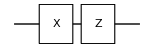

ⅈ S^y

```mathematica
qc=QuissoCircuit[S[1],S[3]]
op=QuissoExpression[qc]
```

This shows more explicitly how Pauli Y “flips” both the bit and phase of the logical basis states.

```mathematica
bs=Basis[S];
out=S[2]**bs;
Thread[bs->out]//LogicalForm//TableForm
```

0_S→ⅈ 1_S
1_S→-ⅈ 0_S

Here is an example how the Pauli Y gate acts on a superposition state.

```mathematica
in=Ket[]c[0]+Ket[S->1]c[1];
in//LogicalForm
out=S[2]**in;
out//LogicalForm
```

c_0 0_S+c_1 1_S

-ⅈ c_1 0_S+ⅈ c_0 1_S

The Pauli gates also correspond, up to a global phase factor (-i), to rotations by the corresponding axes by angle π. Here QuissoRotation[ϕ,S[…,μ]] gives the rotation operator around the μ-axis by angle ϕ.

```mathematica
QuissoRotation[Pi,S[1]]
```

-ⅈ S^x

```mathematica
QuissoRotation[Pi,S[2]]
```

-ⅈ S^y

```mathematica
QuissoRotation[Pi,S[3]]
```

-ⅈ S^z

### Hadamard Gates

The Hadamard gate is represented by S[..., 6] .

```mathematica
S[1,6]
```

S_1^H

Let us consider all the logical basis states.

```mathematica
bs=Basis[S[1]];
bs//LogicalForm
```

{0_S_1,1_S_1}

Operating the Hadamard gate on them gives the two superposition states.

```mathematica
out=S[1,6]**bs;
out//LogicalForm
```

{(0_S_1)/(√2)+(1_S_1)/(√2),(0_S_1)/(√2)-(1_S_1)/(√2)}

In the quantum circuit model, it is denoted by the following circuit element.

```mathematica
QuissoCircuit[S[1,6]]
```

-Graphics-

Geometrically, the Hadamard gate can be regarded as a rotation around the axis (1,0,1) in the Pauli space by angle π.

```mathematica
op=I QuissoRotation[π,S,{1,0,1}]//Garner
mat=Matrix[op];
mat//MatrixForm
```

S^x/(√2)+S^z/(√2)

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

Suppose the Hadamard gates are applied to three qubits.

```mathematica
op=HoldForm@Multiply[S[1,6],S[2,6],S[3,6]]
```

S_1^H S_2^H S_3^H

This shows the overall operation in the quantum circuit model.

```mathematica
qc=QuissoCircuit[S[{1,2,3},6],Null]
```

-Graphics-

Operating the Hadamard gate on each qubit produces a superposition state consisting all logical basis states.

```mathematica
out=ReleaseHold[op]**Ket[];
out//LogicalForm
```

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

This show the same result in the quantum circuit model.

```mathematica
qc=QuissoCircuit[LogicalForm[Ket[],S@{1,2,3}],S[{1,2,3},6]]
QuissoExpression[qc]//LogicalForm
```

-Graphics-

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

Let us compare it with an explicit construction. To do it first prepare the indices of the logical basis states in binary digits.

```mathematica
nn=Range[0,2^3-1];
bit=IntegerDigits[nn,2,3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

This gives an explicit construction (unnormalized) of the superposition of all local basis states.

```mathematica
vec=Total[Ket[S@{1,2,3}->#]&/@bit];
vec//LogicalForm
```

0_S_10_S_20_S_3+0_S_10_S_21_S_3+0_S_11_S_20_S_3+0_S_11_S_21_S_3+1_S_10_S_20_S_3+1_S_10_S_21_S_3+1_S_11_S_20_S_3+1_S_11_S_21_S_3

On other elements of the logical basis, the sign of each term is determined by the bitwise dot product of the its bit-string with that of the input state.

```mathematica
in=Ket[S[{1,2,3}]->{1,0,1}];
in=LogicalForm[in,S@{1,2,3}]
```

1_S_10_S_21_S_3

```mathematica
out=ReleaseHold[op]**in;
out//LogicalForm
```

(0_S_10_S_20_S_3)/(2 √2)-(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)-(0_S_11_S_21_S_3)/(2 √2)-(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)-(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

### Rotations

The Pauli operators are generators of the rotational transformations in a two-dimensional complex vector space, and hence satisfy the fundamental commutation relations of angular momentum operators (up to a normalization factor).

```mathematica
op=S[All]
```

{S^x,S^y,S^z}

```mathematica
in=Outer[HoldForm@*Commutator,op,op];
out=ReleaseHold[in];
Thread[Flatten[in]->Flatten[out]]//TableForm
```

Commutator[S^x,S^x]→0
Commutator[S^x,S^y]→2 ⅈ S^z
Commutator[S^x,S^z]→-2 ⅈ S^y
Commutator[S^y,S^x]→-2 ⅈ S^z
Commutator[S^y,S^y]→0
Commutator[S^y,S^z]→2 ⅈ S^x
Commutator[S^z,S^x]→2 ⅈ S^y
Commutator[S^z,S^y]→-2 ⅈ S^x
Commutator[S^z,S^z]→0

Consider a unitary operator represented by the following matrix.

```mathematica
mat={
{3-I Sqrt[3],I-Sqrt[3]},
{I+Sqrt[3],3+I Sqrt[3]}
}/4;
mat//MatrixForm
```

(1/4 (3-ⅈ √3) | 1/4 (ⅈ-√3)
1/4 (ⅈ+√3) | 1/4 (3+ⅈ √3))

This gives its expression in terms of the Pauli operators.

```mathematica
op=QuissoExpression[mat,S]
```

3/4+(ⅈ S^x)/4-1/4 ⅈ √3 S^y-1/4 ⅈ √3 S^z

```mathematica
Dagger[op]**op
```

1

This gives the Euler angles of the unitary operator.

```mathematica
angs=TheEulerAngles[mat]
```

{π/3,π/3,0}

Indeed, the Euler angles reproduces the original unitary operator.

```mathematica
new=QuissoEulerRotation[angs,S]
op-new
```

3/4+(ⅈ S^x)/4-1/4 ⅈ √3 S^y-1/4 ⅈ √3 S^z

0

## Two-Qubit Gates

### CNOT and CZ

CNOT[control, target] denotes the CNOT gate in the quantum circuit model.

```mathematica
op=CNOT[S[1],S[2]]
```

CNOT[{S_1},{S_2}]

This displays the quantum circuit model of the CNOT gate.

```mathematica
qc=QuissoCircuit[op]
```

-Graphics-

This is the explicit expression of the CNOT gate in terms of the Pauli operators.

```mathematica
op=QuissoExpression[qc]
```

1/2-1/2 S_1^z S_2^x+S_1^z/2+S_2^x/2

This is the matrix representation of the CNOT gate in the logical basis.

```mathematica
Matrix[op]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

This shows how the CNOT gate operates on the logical basis states.

```mathematica
in=Basis[S@{1,2}];
out=op**in;
Thread[in->out]//LogicalForm//TableForm
```

0_S_10_S_2→0_S_10_S_2
0_S_11_S_2→0_S_11_S_2
1_S_10_S_2→1_S_11_S_2
1_S_11_S_2→1_S_10_S_2

As an example of the application of the CNOT gate, this shows an entangler quantum circuit.

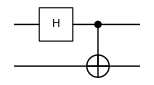

```mathematica
entangler=QuissoCircuit[S[1,6],CNOT[S[1],S[2]]]
```

This demonstrates the generation of an entangled state from a product state.

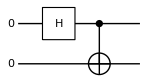

(0_S_10_S_2)/(√2)+(1_S_11_S_2)/(√2)

```mathematica
new=QuissoCircuit[LogicalForm[Ket[S@{1,2}->{0,0}],S@{1,2}],entangler]
vec=QuissoExpression[new];
vec//LogicalForm
```

This lists the mapping between the standard tensor-product basis states and the Bell states.

```mathematica
bs=Basis@S@{1,2};
op=QuissoExpression[entangler];
out=op**bs;
table=Thread[bs->out];
table//LogicalForm//TableForm
```

0_S_10_S_2→(0_S_10_S_2)/(√2)+(1_S_11_S_2)/(√2)
0_S_11_S_2→(0_S_11_S_2)/(√2)+(1_S_10_S_2)/(√2)
1_S_10_S_2→(0_S_10_S_2)/(√2)-(1_S_11_S_2)/(√2)
1_S_11_S_2→(0_S_11_S_2)/(√2)-(1_S_10_S_2)/(√2)

Solution: To generate a maximally entangled state between two two-qubit registers.

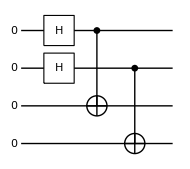

```mathematica
qc=QuissoCircuit[LogicalForm[Ket[],S@{1,2,3,4}],S[{1,2},6],CNOT[S[1],S[3]],CNOT[S[2],S[4]],PlotRangePadding->0,ImagePadding->{{36,36},{5,5}}]
```

```mathematica
qc=QuissoCircuit[LogicalForm[Ket[],S@{1,2,3,4}],S[{1,2},6],CNOT[S[1],S[3]],CNOT[S[2],S[4]]]
```

-Graphics-

```mathematica
out=QuissoExpression[qc];
out//LogicalForm
```

1/2 0_S_10_S_20_S_30_S_4+1/2 0_S_11_S_20_S_31_S_4+1/2 1_S_10_S_21_S_30_S_4+1/2 1_S_11_S_21_S_31_S_4

This example illustrate that the entanglement depends on the partition of the system. Indeed, the above system is a product state for the partition (1,3) and (2,4) qubits.

```mathematica
QuissoFactor[out]
```

1/2 (0_S_10_S_3+1_S_11_S_3)⊗(0_S_20_S_4+1_S_21_S_4)

The above construction can be generalized for a pair of n-qubit systems.

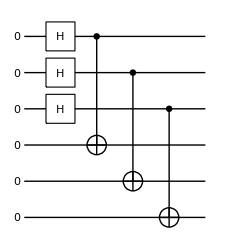

```mathematica
n=3;
qc=QuissoCircuit[LogicalForm[Ket[],S@Range[2n]],S[Range[n],6],Sequence@@Table[CNOT[S[j],S[n+j]],{j,1,n}]]
```

```mathematica
out=QuissoExpression[qc];
out//LogicalForm
```

(0_S_10_S_20_S_30_S_40_S_50_S_6)/(2 √2)+(0_S_10_S_21_S_30_S_40_S_51_S_6)/(2 √2)+(0_S_11_S_20_S_30_S_41_S_50_S_6)/(2 √2)+(0_S_11_S_21_S_30_S_41_S_51_S_6)/(2 √2)+(1_S_10_S_20_S_31_S_40_S_50_S_6)/(2 √2)+(1_S_10_S_21_S_31_S_40_S_51_S_6)/(2 √2)+(1_S_11_S_20_S_31_S_41_S_50_S_6)/(2 √2)+(1_S_11_S_21_S_31_S_41_S_51_S_6)/(2 √2)

The CZ (or controlled-Z) gate is a variant of the CNOT gate.

```mathematica
op=CZ[S[1],S[2]]
```

CZ[S_1,S_2]

This shows how it transforms the logical basis states.

```mathematica
bs=Basis@S@{1,2};
out=op**bs;
Thread[bs->out]//LogicalForm//TableForm
```

0_S_10_S_2→0_S_10_S_2
0_S_11_S_2→0_S_11_S_2
1_S_10_S_2→1_S_10_S_2
1_S_11_S_2→-1_S_11_S_2

Here is the matrix representation of the CZ gate.

```mathematica
mat=Matrix[Elaborate@op];
mat//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

This is the quantum circuit model of the CZ gate.

```mathematica
cz=QuissoCircuit[CZ[S[1],S[2]]]
```

-Graphics-

Note the following identity.

```mathematica
expr=HoldForm[S[1,6]**S[1,3]**S[1,6]==S[1,1]]
ReleaseHold[expr]//Elaborate
```

S_1^H**S_1^z**S_1^H==S_1^x

True

It leads to the following relation between the CNOT gate and CZ gate.

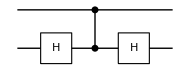

```mathematica
new=QuissoCircuit[S[2,6],cz,S[2,6]]
```

```mathematica
cnot=QuissoCircuit[CNOT[S[1],S[2]]]
```

-Graphics-

```mathematica
Elaborate[new]-Elaborate[cnot]
```

0

### Controlled-U Gates

Consider a single-qubit rotation acting on the qubit S[2,None]. It is a rotation around the y-axis by angle ϕ.

```mathematica
U=Rotation[ϕ,S[2,2],"Label"->"U"];
U//Elaborate//Matrix//MatrixForm
```

(Cos[ϕ/2] | -Sin[ϕ/2]
Sin[ϕ/2] | Cos[ϕ/2])

This shows the controlled-U gate.

```mathematica
qc=QuissoCircuit[ControlledU[S[1],U]]
```

-Graphics-

```mathematica
op=QuissoExpression[qc]
```

Cos[ϕ/4]^2+S_1^z Sin[ϕ/4]^2+1/2 ⅈ S_1^z S_2^y Sin[ϕ/2]-1/2 ⅈ S_2^y Sin[ϕ/2]

When the first qubit is set to Ket[0], it does nothing.

```mathematica
Let[Complex,c]
vec=Ket[]c[0]+Ket[S[2]->1]c[2];
LogicalForm[vec,S@{1,2}]
```

c_0 0_S_10_S_2+c_2 0_S_11_S_2

```mathematica
new=op**vec;
LogicalForm[new,S@{1,2}]
```

c_0 0_S_10_S_2+c_2 0_S_11_S_2

When the control qubit -- the first qubit in this case -- is set to Ket[1], it operates the unitary operator on the second qubit.

```mathematica
vec=Ket[S[1]->1]**(Ket[]c[0]+Ket[S[2]->1]c[2]);
LogicalForm[vec,S@{1,2}]
```

c_0 1_S_10_S_2+c_2 1_S_11_S_2

```mathematica
new=op**vec;
LogicalForm[new,S@{1,2}]
```

1_S_11_S_2 (c_2 Cos[ϕ/2]+c_0 Sin[ϕ/2])+1_S_10_S_2 (c_0 Cos[ϕ/2]-c_2 Sin[ϕ/2])

When the control qubit  is in a superposition, the resulting state is an entangled state in general.

```mathematica
vec=Ket[]+Ket[S[1]->1];
LogicalForm[vec,S@{1,2}]
```

0_S_10_S_2+1_S_10_S_2

```mathematica
new=op**vec;
LogicalForm[new,S@{1,2}]
```

0_S_10_S_2+Cos[ϕ/2] 1_S_10_S_2+1_S_11_S_2 Sin[ϕ/2]

When the target qubit is set to an eigenstate of the unitary operator, it does not change but the control qubit acquires the phase factor given by the eigenvalue of the target state.

```mathematica
vec=(Ket[]+Ket[S[1]->1])**(Ket[]-I Ket[S[2]->1]);
LogicalForm[QuissoFactor@vec,S@{1,2}]
```

(0_S_1+1_S_1)⊗(0_S_2-ⅈ 1_S_2)

```mathematica
new=op**vec//TrigToExp;
LogicalForm[QuissoFactor@new,S@{1,2}]
```

(0_S_1+ⅇ^((ⅈ ϕ)/2) 1_S_1)⊗(0_S_2-ⅈ 1_S_2)

Solution: The eigenstates of U are the same as those of Pauli[1].

```mathematica
U=Rotation[ϕ,S[1,1]]//Elaborate
```

Cos[ϕ/2]-ⅈ S_1^x Sin[ϕ/2]

```mathematica
vec=S[1,6]**Ket[];
vec//LogicalForm
```

(0_S_1)/(√2)+(1_S_1)/(√2)

```mathematica
U**vec//LogicalForm//TrigToExp//Simplify
```

(ⅇ^(-(ⅈ ϕ)/2) (0_S_1+1_S_1))/(√2)

```mathematica
vec=S[1,6]**Ket[S[1]->1];
vec//LogicalForm
```

(0_S_1)/(√2)-(1_S_1)/(√2)

```mathematica
U**vec//LogicalForm//TrigToExp//Simplify
```

(ⅇ^((ⅈ ϕ)/2) (0_S_1-1_S_1))/(√2)

The ancillary qubit takes a relative phase shift depending on in which eigenstate the native qubit is.

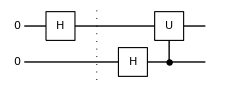

```mathematica
Let[Real,ϕ];
qc=QuissoCircuit[LogicalForm[Ket[],S@{1,2}],S[1,6],"Separator",S[2,6],ControlledU[S[2],Rotation[ϕ,S[1,1]],"Label"->"U"]]
```

```mathematica
out=QuissoExpression[qc]//TrigToExp;
LogicalForm[QuissoFactor@out,S@{1,2}]
```

1/2 ⅇ^(-(ⅈ ϕ)/2) (0_S_1+1_S_1)⊗(ⅇ^((ⅈ ϕ)/2) 0_S_2+1_S_2)

Make a basis change to detect it.

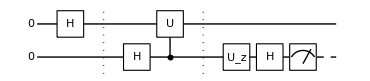

```mathematica
qc=QuissoCircuit[LogicalForm[Ket[],S@{1,2}],S[1,6],"Separator",S[2,6],ControlledU[S[2],Rotation[ϕ,S[1,1]],"Label"->"U"],"Separator",Rotation[ϕ/2,S[2,3]],S[2,6],Measurement[S[2]]]
```

```mathematica
out=QuissoExpression[qc]//TrigToExp;
LogicalForm[QuissoFactor@out,S@{1,2}]
```

(ⅇ^(-(ⅈ ϕ)/4) (0_S_10_S_2+1_S_10_S_2))/(√2)

Solution: This constructs the desired quantum circuit model.

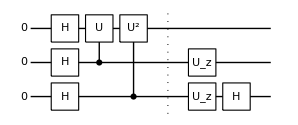

```mathematica
qc=QuissoCircuit[LogicalForm[Ket[],S@{1,2,3}],S[{1,2,3},6],ControlledU[S[2],Rotation[ϕ,S[1,1]],"Label"->"U"],ControlledU[S[3],Rotation[2ϕ,S[1,1]],"Label"->"U^2"],"Separator",{Rotation[0,S[2,3]],Rotation[Pi/2,S[3,3]]},S[3,6]]
```

```mathematica
out=QuissoExpression[qc]//TrigToExp//Simplify;
LogicalForm[QuissoFactor@out/.ϕ->Pi/2,S@{1,2}]
```

((1/4+ⅈ/4) ⅇ^(-(3 ⅈ π)/4) (0_S_1+1_S_1)⊗(ⅇ^((ⅈ π)/4) 0_S_2+1_S_2)⊗(2 0_S_3))/(√2)

Consider a controlled-U gate.

```mathematica
matU=RandomUnitary[2];
matU//MatrixForm
```

(-0.179484-0.983393 ⅈ | -0.0260325-0.00682446 ⅈ
-0.0198922+0.0181263 ⅈ | -0.297389-0.954377 ⅈ)

```mathematica
opU=QuissoExpression[matU,S[2]];
qc1=QuissoCircuit[ControlledU[S[1],opU,"Label"->"U"]]
```

-Graphics-

For the decomposition, first find the Euler angles of the unitary operator.

```mathematica
detU=Det[matU];
vphi=Arg[detU]/2;
{a,b,c}=TheEulerAngles[matU/Sqrt[detU]]
```

{4.15394,0.0538308,2.00771}

From the Euler angles, choose the component operators.

```mathematica
opA=EulerRotation[{a,b/2,0},S[2],"Label"->"A"];
opB=EulerRotation[{0,-b/2,-(a+c)/2},S[2],"Label"->"B"];
opC=EulerRotation[{0,0,-(a-c)/2},S[2],"Label"->"C"];
opD=Phase[vphi,S[1]];
```

Finally, construct the equivalent quantum circuit model.

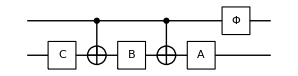

```mathematica
qc2=QuissoCircuit[opC,CNOT[S[1],S[2]],opB,CNOT[S[1],S[2]],opA,opD]
```

Check the result.

```mathematica
QuissoExpression[qc1]-QuissoExpression[qc2]//Chop
```

0

### General Unitary Gates

Consider a Hermitian operator on a two-qubit system. Physically, it corresponds to a transverse-field Ising model.

```mathematica
H=S[1,1]**S[2,1]+S[1,2]+S[2,2]+S[1,3]+S[2,3]
matH=Matrix[H];
matH//MatrixForm
```

S_1^x S_2^x+S_1^y+S_1^z+S_2^y+S_2^z

(2 | -ⅈ | -ⅈ | 1
ⅈ | 0 | 1 | -ⅈ
ⅈ | 1 | 0 | -ⅈ
1 | ⅈ | ⅈ | -2)

This is the unitary operator generated by the above Hermitian operator.

```mathematica
U=MultiplyExp[-I  H Pi/4]
```

ⅇ^(-1/4 ⅈ π (S_1^x S_2^x+S_1^y+S_1^z+S_2^y+S_2^z))

This shows the matrix representation of U in the logical basis.

```mathematica
matU=Matrix[U]//Simplify;
matU//MatrixForm
```

(-(1/2+(5 ⅈ)/6)/(√2) | -(1/6-ⅈ/2)/(√2) | -(1/6-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2)
(1/6-ⅈ/2)/(√2) | (1/2+ⅈ/6)/(√2) | -(1/2+(5 ⅈ)/6)/(√2) | -(1/2+ⅈ/2)/(√2)
(1/6-ⅈ/2)/(√2) | -(1/2+(5 ⅈ)/6)/(√2) | (1/2+ⅈ/6)/(√2) | -(1/2+ⅈ/2)/(√2)
(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2))

This shows the decomposition of the unitary matrix into two-level matrices (displaying the first three elements). For the purpose of efficiency, the resulting list is given in terms of TwoLevelU.

```mathematica
twl=TwoLevelDecomposition[matU]//Simplify;
twl[[;;3]]
```

{TwoLevelU[{{1,0},{0,1}},{3,4},4],TwoLevelU[{{(1/2-(3 ⅈ)/2)/(√7),-(3/2+(3 ⅈ)/2)/(√7)},{(3/2-(3 ⅈ)/2)/(√7),(1/2+(3 ⅈ)/2)/(√7)}},{3,4},4],TwoLevelU[{{-(1-3 ⅈ)/(√38),√(14/19)},{-√(14/19),-(1+3 ⅈ)/(√38)}},{2,3},4]}

For a more intuitive form, you can convert TwoLevelU into the normal matrix form using Matrix. Here the first three are shown.

```mathematica
MatrixForm/@Matrix/@twl[[;;3]]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | (1/2-(3 ⅈ)/2)/(√7) | -(3/2+(3 ⅈ)/2)/(√7)
0 | 0 | (3/2-(3 ⅈ)/2)/(√7) | (1/2+(3 ⅈ)/2)/(√7)),(1 | 0 | 0 | 0
0 | -(1-3 ⅈ)/(√38) | √(14/19) | 0
0 | -√(14/19) | -(1+3 ⅈ)/(√38) | 0
0 | 0 | 0 | 1)}

Indeed, they reconstruct the original matrix.

```mathematica
new=Dot@@Matrix/@twl;
matU-new//Simplify//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Consider a two-level matrix of the form.

```mathematica
matU=TheHadamard[];
code=TwoLevelU[matU,{3,4},4];
full=Matrix[code];
full//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1/(√2) | 1/(√2)
0 | 0 | 1/(√2) | -1/(√2))

It corresponds to a single controlled-U gate.

```mathematica
ctrlU=GrayTwoLevelU[matU,{3,4},S@{1,2}];
QuissoCircuit[ctrlU]
```

-Graphics-

Consider a two-level matrix of the form.

```mathematica
matU=TheHadamard[];
code=TwoLevelU[matU,{2,4},4];
full=Matrix[code];
full//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1/(√2) | 0 | 1/(√2)
0 | 0 | 1 | 0
0 | 1/(√2) | 0 | -1/(√2))

It corresponds to a single controlled-U gate with the control and target qubit exchanged.

```mathematica
ctrlU=GrayTwoLevelU[matU,{2,4},S@{1,2}];
QuissoCircuit[ctrlU]
```

-Graphics-

Consider a two-level matrix of the form.

```mathematica
matU=TheHadamard[];
code=TwoLevelU[matU,{2,3},4];
full=Matrix[code];
full//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1/(√2) | 1/(√2) | 0
0 | 1/(√2) | -1/(√2) | 0
0 | 0 | 0 | 1)

In this case, we need to apply the CNOT gate before and after the controlled-U gate.

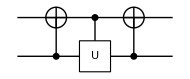

```mathematica
ctrlU=GrayTwoLevelU[matU,{2,3},S@{1,2}];
QuissoCircuit[ctrlU]
```

Consider a two-level matrix of the form.

```mathematica
matU=TheHadamard[];
code=TwoLevelU[matU,{1,4},4];
full=Matrix[code];
full//MatrixForm
```

(1/(√2) | 0 | 0 | 1/(√2)
0 | 1 | 0 | 0
0 | 0 | 1 | 0
1/(√2) | 0 | 0 | -1/(√2))

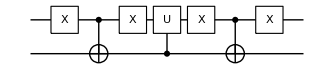

```mathematica
ctrlU=GrayTwoLevelU[matU,{1,4},S@{1,2}];
QuissoCircuit@@ctrlU
```

Let us consider again the two-qubit model demonstrated before.

```mathematica
H=S[1,1]**S[2,1]+S[1,2]+S[2,2]+S[1,3]+S[2,3]
U=MultiplyExp[-I  H Pi/4]
matU=Matrix[U];
```

S_1^x S_2^x+S_1^y+S_1^z+S_2^y+S_2^z

ⅇ^(-1/4 ⅈ π (S_1^x S_2^x+S_1^y+S_1^z+S_2^y+S_2^z))

This is the decomposition into the two-level matrices, just showing the first four.

```mathematica
twl=TwoLevelDecomposition[matU]//Simplify;
MatrixForm/@Matrix/@twl[[;;3]]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | (1/2-(3 ⅈ)/2)/(√7) | -(3/2+(3 ⅈ)/2)/(√7)
0 | 0 | (3/2-(3 ⅈ)/2)/(√7) | (1/2+(3 ⅈ)/2)/(√7)),(1 | 0 | 0 | 0
0 | -(1-3 ⅈ)/(√38) | √(14/19) | 0
0 | -√(14/19) | -(1+3 ⅈ)/(√38) | 0
0 | 0 | 0 | 1)}

The two-level matrices are written in terms of the controlled-U and CNOT gate, again showing the first four. The first of the list twl happens to be the identity matrix in this case, and it is excluded in the further analysis.

```mathematica
gates=GrayTwoLevelU[#,S@{1,2}]&/@Rest[twl];
gates[[;;3]]
```

{{ControlledU[{S_1},1/(2 √7)-(3 ⅈ S_2^x)/(2 √7)-(3 ⅈ S_2^y)/(2 √7)-(3 ⅈ S_2^z)/(2 √7),Label→U]},{CNOT[{S_2},{S_1}],ControlledU[{S_1},-1/(√38)-ⅈ √(14/19) S_2^y-(3 ⅈ S_2^z)/(√38),Label→U],CNOT[{S_2},{S_1}]},{ControlledU[{S_1},-5/(14 √2)+3/14 ⅈ √19 S_2^y-(5 ⅈ S_2^z)/(14 √2),Label→U]}}

This shows the overall quantum circuit model. Here the same label “U” has been used for different controlled-U gates just for 
convenience. Do not forget to reverse the order before plugging the gates in the quantum circuit model.

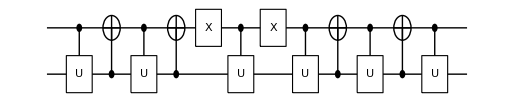

```mathematica
qc=QuissoCircuit@@Reverse@Flatten[gates]
```

Check the above quantum circuit by converting it into the matrix representation.

```mathematica
new=Matrix[qc]//Simplify;
new//MatrixForm
```

(-(1/2+(5 ⅈ)/6)/(√2) | -(1/6-ⅈ/2)/(√2) | -(1/6-ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2)
(1/6-ⅈ/2)/(√2) | (1/2+ⅈ/6)/(√2) | -(1/2+(5 ⅈ)/6)/(√2) | -(1/2+ⅈ/2)/(√2)
(1/6-ⅈ/2)/(√2) | -(1/2+(5 ⅈ)/6)/(√2) | (1/2+ⅈ/6)/(√2) | -(1/2+ⅈ/2)/(√2)
(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | -(1/2-ⅈ/2)/(√2))

```mathematica
new-matU//Simplify//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

## Multi-Qubit Controlled Gates

This is a three-qubit controlled-U gate.

```mathematica
qc=QuissoCircuit[ControlledU[S@{1,2,3},S[4,1],"Label"->"U"]]
```

-Graphics-

### Gray Code

Consider a three-qubit register as an example.

```mathematica
$L=3;
jj=Range[$L];
cc=S[jj,None];
```

This is the gate to operate on the target qubit.

```mathematica
T=S[$L+1,None];
op=QuissoRotation[Pi/3,T[1]]
```

(√3)/2-(ⅈ S_4^x)/2

This decomposes the multi-qubit controlled-U gate based on the Gray code -- showing only a part of it. Each component is either CNOT or a two-qubit controlled-U gate.

```mathematica
gc=GrayControlledU[cc,op]; gc[[;;3]]
```

{ControlledU[{S_1},(2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24))/(2 2^(1/4))+((2^(1/4) ⅇ^(-(ⅈ π)/24)-2^(1/4) ⅇ^((ⅈ π)/24)) S_4^x)/(2 2^(1/4)),Label→V],CNOT[{S_1},{S_2}],ControlledU[{S_2},(2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24))/(2 2^(1/4))+((-2^(1/4) ⅇ^(-(ⅈ π)/24)+2^(1/4) ⅇ^((ⅈ π)/24)) S_4^x)/(2 2^(1/4)),Label→V^†]}

This is a quantum circuit model of the decomposition.

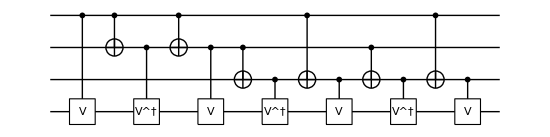

```mathematica
qc=QuissoCircuit[gc]
```

Finally check the result.

```mathematica
expr=QuissoExpression[qc];
expr2=QuissoControlledU[cc,op];
expr-expr2//Garner
```

0

### Multi-Qubit Controlled-NOT

This shows a generalized CNOT gate, controlled by three qubits rather than a single qubit.

```mathematica
qc=QuissoCircuit[CNOT[S@{1,2,3},S[4]]]
```

-Graphics-

Here is the explicit expression of the multi-qubit CNOT gate in terms of the Pauli operators.

```mathematica
op=QuissoExpression[qc]
```

7/8-1/8 S_1^z S_2^z-1/8 S_1^z S_3^z-1/8 S_1^z S_4^x-1/8 S_2^z S_3^z-1/8 S_2^z S_4^x-1/8 S_3^z S_4^x+1/8 S_1^z S_2^z S_3^z+1/8 S_1^z S_2^z S_4^x+1/8 S_1^z S_3^z S_4^x+1/8 S_2^z S_3^z S_4^x-1/8 S_1^z S_2^z S_3^z S_4^x+S_1^z/8+S_2^z/8+S_3^z/8+S_4^x/8

Here we compare it with the expression explicitly constructed in terms of a projection operator.

```mathematica
prj=Multiply@@S[{1,2,3},11];
new=(1-prj)+prj**S[4,1]
op-new//Elaborate
```

1-(11)_S_1(11)_S_2(11)_S_3+(11)_S_1(11)_S_2(11)_S_3 S_4^x

0

## Universal Quantum Computation

## Measurement

First consider a measurement in the logical basis.

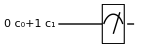

```mathematica
Let[Complex,c]
vec=ProductState[S[1]->{c[0],c[1]}];
qc=QuissoCircuit[vec,"Spacer",Measurement[S[1]],PlotRangePadding->{{2,0},None}]
```

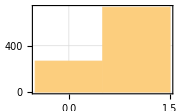

```mathematica
Block[
{c,data},
c[0]=1/2;
c[1]=Sqrt[3]/2;
data=Table[out=QuissoExpression[qc];Readout[out,S[1]],1000];
Histogram[data,FrameLabel->{"Readout","Counts"},ImageSize->Small]
]
```

Now consider a measurement in the eigen-basis of the Pauli X operator.

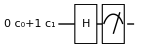

```mathematica
Let[Complex,c]
vec=ProductState[S[1]->{c[0],c[1]}];
qc=QuissoCircuit[vec,S[1,6],Measurement[S[1]],PlotRangePadding->{{2,0},None}]
```

```mathematica
Block[
{c,data},
c[0]=1/2;
c[1]=Sqrt[3]/2;
data=Table[out=QuissoExpression[qc];Readout[out,S[1]],1000];
Histogram[data,FrameLabel->{"Readout","Counts"},ImageSize->Small]
]
```

$Aborted

This is the "disentangler" quantum circuit, which is the inverse of the entangler quantum circuit .

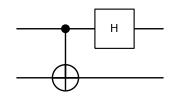

```mathematica
disentangler=QuissoCircuit[CNOT[S[1],S[2]],S[1,6],ImageSize->Small]
```

This shows that the disentangler quantum circuit maps the Bell states into the logical basis states.

```mathematica
op=QuissoExpression[disentangler];
bs=BellState@S@{1,2};
Thread[bs->op**bs]//LogicalForm//TableForm
```

(0_S_10_S_2+1_S_11_S_2)/(√2)→0_S_10_S_2
(0_S_11_S_2+1_S_10_S_2)/(√2)→0_S_11_S_2
(0_S_11_S_2-1_S_10_S_2)/(√2)→1_S_11_S_2
(0_S_10_S_2-1_S_11_S_2)/(√2)→1_S_10_S_2

As an example, consider a two-qubit quantum state.

```mathematica
vec=Ket[]+I Ket[S[1]->1]+Ket[S[2]->1];
vec//LogicalForm
```

0_S_10_S_2+0_S_11_S_2+ⅈ 1_S_10_S_2

This is a full quantum circuit model to perform the Bell measurement on the state specified above.

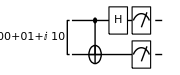

```mathematica
qc=QuissoCircuit[vec,disentangler,Measurement@S@{1,2},PlotRangePadding->{{2,0},None}]
```

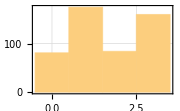

```mathematica
data=Table[out=QuissoExpression[qc];FromDigits[Readout[out,S@{1,2}],2],500];
Histogram[data,FrameLabel->{"Readout","Counts"},ImageSize->Small]
```